given a table of n values

-Graphics-

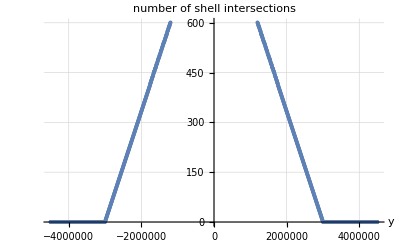

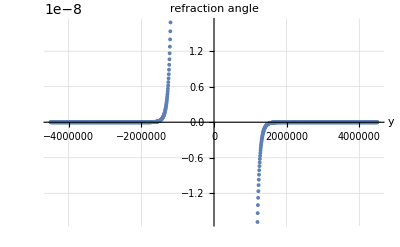

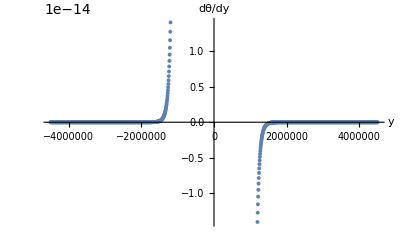

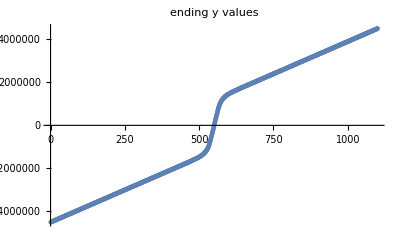

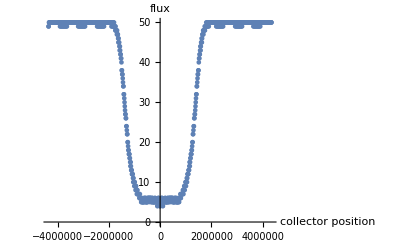

runtime: 4239.2407017

```mathematica
Clear["Global`*"];
startTime = SessionTime[];

(* Assumptions:
 shells are located around the origin
light rays never bend more than 90 degrees
*)

(* local gravity as a function of r *)
Gravity[r_]:=G*MPluto/r^2;

(* pressure as a function of height *)
Pressure[p0_,M_,h_,T_]:=p0 E^((-M Gravity[h+rSurf] h)/(k T));

(* Lorentz-Lorenz Equation for n values close to 1: returns a refractive index n given a temperature and pressure*)
LorentzLorenz[α_,p_,T_]:=√(1+(4π NAvagadro α p)/(R T)); 

(* indicies of refraction following the fit for the numbers provided in EY92 *)
EY92[r_]:=SetPrecision[1+2*10^105 r^-18.75,15];

(* shells are composed of the following: the circle graphic, the circle equation, the circle radius, the n value, and the attenuation coefficient αz *)
(* note that attenuation coefficient is represented here as αz rather than α because the letter also stands for mean polarizability, which is used elsewhere in this program; αz implies it's a function of z- the distance the beam of light travelled in the material *)
Shell[r_,n_,αz_]:={Circle[{0,0},r],x^2+y^2==r^2,r,n,αz}; 

(* calculate the normal angle of a shell based on location, assuming shells centered at 0,0) *)
NormalAngle[point_]:=ArcTan[point[[1]],point[[2]]]; 

(* helper function to negate the y term of an xy pair for flipping atmospheric intersection points *)
FlipY[x_,y_]:=Return[{x,-y}];

(* refraction as a function of angles and rafractivity indicies *)
SnellsLaw[θin_,nin_,nout_]:=
If[nin == nout,
θin,
ArcSin[Sin[θin]nin/nout]
];

(* make an atmosphere with linearly-spaced shells specified by minimum, maximum, and step size of radius *)
MakeAtmosphere[min_,max_,step_,nTable_,αzTable_]:=Module[{r,center,nMax,nStep,n,αz,i},
atmosphere={};

Which[
(* if nTable is null, use a linearly-varying n with nMax == 1.01 *)
((Length[nTable]==0)),
{
Print["not given a table of n values"];
If[nTable==Null,
nMax = 1.01;
];
If[NumberQ[nTable],
nMax = nTable;
];

nStep = (nMax-1.)/((max-min+1)/step); (*+1 is to ensure that the outer shell doesn't have n = 1.0 *)
n = nMax;
Do[
{
atmosphere =Append[atmosphere,Shell[r,n]];
n-=nStep;
},
{r,min,max,step}
];
},

True,
(* we're actually given a table of n values *)
{
Print["given a table of n values"],
i = 1;
Do[
{
n=nTable[[i]];
atmosphere =Append[atmosphere,Shell[r,n,αz]];
i+=1;
},
{r,min,max,step}
];
}
]
]

(* make the graphics objects *)
MakeAtmosphereGraphic[atm_]:=Table[Graphics[{Opacity[0.5],Thin,atmosphere[[i,1]]}],{i,1,Length[atm]}];

MakeIntersectionsPointsGraphic[intersections_]:=Graphics[{Red,Point[Table[{x/.intersections[[i]],y/.intersections[[i]]},{i,Length[intersections]}]]}];

FindNextShellIntersection[radius_,rayPosition_,rayAngle_]:=Module[{x0,y0,m,t1,t2,tList},
x0 = rayPosition[[1]];
y0 = rayPosition[[2]];
m=Tan[rayAngle];
t1 = (-x0-m y0 + √(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);
t2 = (-x0-m y0 - √(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);

(* return only real positive time values *)
tList=Select[{t1,t2},(#∈Reals&&#>TOL)&]
]

(* function that identifies where the light currently is in relation to shells *)
LocateLightRay[position_,atm_]:=Module[{shellRadii,posRadius,difference,shellNum},
{
shellRadii = atm[[All,3]];
posRadius = Norm[position];
Which[
(* entirely outside of shells *)
posRadius > Last[shellRadii],
rayLocation = "outside",

(* entirely inside the inner shell *)
posRadius < First[shellRadii],
rayLocation = "inside",

(* on outer shell *)
Abs[Last[shellRadii]- posRadius]<TOL,
rayLocation = "on outer shell",

True,
{
Do[
difference = Abs[posRadius-shellRadii[[i]]];
If[difference<TOL,
shellNum = i;
rayLocation="on";
Break[];,
rayLocation = "between";
];,
{i,Length[atm]}
]
}
]
};
rayLocation
]

(* updates the light position based on current position, direction, and shells *)
MoveLightRay[rayPath_,rayAngle_,atm_]:=Module[{location,tList,intersect,t,n2,αz,position,posRadius,shellNum,noIntersect,atEnd},
extincted = False;
position = Last[rayPath];
posRadius = Norm[position];

location  = LocateLightRay[position,atm];
Which[
(* only need to check the outermost shell *)
location == "outside",
{
t = Min[FindNextShellIntersection[Last[atm][[3]],position,rayAngle]];
},

(* only need to check the innermost shell *)
location == "inside",
{
t = Min[FindNextShellIntersection[First[atm][[3]],position,rayAngle]];
},

(* only need to check the second-outermost and itself shell unless it's a one-shell atmosphere *)
location == "on outer shell",
{
If[Length[atm]>1,
(* if it's a multi-shell atmosphere *)
{
t = Min[Join[
FindNextShellIntersection[atm[[-2,3]],position,rayAngle],
FindNextShellIntersection[atm[[-1,3]],position,rayAngle]
]
];
},

(* else if it's a single-shell atmosphere *)
{
t = Min[FindNextShellIntersection[atm[[1,3]],position,rayAngle]];
}
]
},

(* need to check the previous, current, and next shells *)
location == "on",
{
Do[
If[Abs[posRadius-atm[[All,3]][[i]]]<TOL,
shellNum = i;
Break[];,
];,
{i,Length[atm]}
];

If[shellNum==1,
(* if on inner shell - the innermost shell represents the planet itself *)
{
extincted = True;
t =0;
},

(* if on some other shell *)
t = Min[Join[
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum-1,3]],position,rayAngle]
]
]
];
},

(* need to check the shells that it is between- now use currentShell as a counter *)
location == "between",
{
Print["warning: between atmosphere layers - this shouldn't really happen"];
shellNum =Length[atm];
While[atm[[shellNum,3]] > posRadius,
shellNum-=1; 
];
tList = Join[
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle]
];
t= Min[tList];
}
];

(* stuff to be done regardless of ray location case *)

(* check for non-intersection case *)
noIntersect = False;
atEnd = False;
If[t==Infinity,
If[Length[rayPath]==1,
noIntersect = True;
];
atEnd = True;
t=distToObserver; (* move the end of the light beam to the observer position *)
];

intersect = {t+position[[1]],Tan[rayAngle ] t + position[[2]]};
position = intersect;

(* figure out which we're now interacting with *)
Do[
If[Abs[Norm[position]-atm[[All,3]][[i]]]<TOL,
(* get the refractivity of the shell *)
n2 = atm[[i,4]];
αz=atm[[i,5]];
Break[];,

(* if we're not interacting with a shell, then we're back in vacuum with n2 = 1.0 and αz = 0*)
n2 = 1.0;
αz=0;
];,
{i,Length[atm]}
];

(* if the light has not been entirely extincted yet, append the angle and final flux level to the appropriate lists *)
If[!extincted,
AppendTo[intersectionPoints,position];
Which[noIntersect,
AppendTo[angleList,0.0];
AppendTo[finalFlux,1.0];,

atEnd,
AppendTo[angleList,rayAngle];
AppendTo[finalFlux,currentRayFlux];,

True,
AppendTo[angleList,Refract[intersectionPoints,angleList,n2]];
AppendTo[finalFlux,BeerLambert[αz,currentRayFlux,1.0]]; (*TODO - currently arbitrarily setting z = 1, need to put in real values *) 
];

position
];
];

(* refract based on entry and shell conditions using Snell's Law *)
Refract[rayPath_,angles_,n2_]:=Module[{newAngle,position,prevPosition,θ1,θ2,angle,interactionType},
position = Last[rayPath];
prevPosition = rayPath[[-2]];
angle = Last[angles];
interactionType = Null;

Which[
(* hitting the same shell again -- wait, I shouldn't actually need this, it should be included in the Snell's Law function *)
currentN==n2,
{
interactionType = "same shell";
newAngle = angle;
},

(* just grazed the top or bottom of a shell (no interaction), keep the angle the same *)
Abs[position[[1]]]<TOL,
{
interactionType = "grazed";
newAngle = angle;
(*Print["grazed shell with angle = " <> ToString[angle] <>" and starting y value of " <> ToString[yStart]];*)
},

(* hitting shell from outside in (radius decreasing) *)
Norm[position]<Norm[prevPosition],
{
interactionType = "outside in";

If [position[[2]]>0,
{ (* above the y = 0 line *)
θ1= Mod[π-NormalAngle[position]+angle,π/2];
θ2=SnellsLaw[θ1,currentN,n2];
newAngle = NormalAngle[position]-π+θ2;
},
{ (* on or below the y = 0 line *)
θ1=Mod[NormalAngle[position]-π-angle,π/2];
θ2=SnellsLaw[θ1,currentN,n2];
newAngle = NormalAngle[position]-π-θ2;
}
]
},

(* hitting shell from inside out *)
Norm[position]>Norm[prevPosition] || Norm[position]== Norm[prevPosition],
{
interactionType = "outside in";

If[position[[2]]>0,
{ (* above the y = zero line *)
θ1=Mod[NormalAngle[position]-angle,π/2];
θ2=SnellsLaw[θ1,currentN,n2];
newAngle = NormalAngle[position]-θ2;
},
{ (* on or below the y = 0 line *)
θ1=Mod[angle-NormalAngle[position],π/2];
θ2=SnellsLaw[θ1,currentN,n2];
newAngle = NormalAngle[position]+θ2;
}
]
}
];
If[interactionType ≠ "grazed",
currentN=n2;
];

newAngle = Re[newAngle]; (* tiny imaginary portion sometimes makes it into the newAngle- this is the sketchy way out *)

newAngle = Mod[newAngle,2*π];
(* TODO - probably more elegent way to do the angle formatting, because I basically want all angles to be near zero for readability *)
If[newAngle> 3*π/4,
newAngle = newAngle-2*π;
];

newAngle
];

(* decrease the flux of a single light beam based on the linear approximation of the Beer-Lambert law *)
BeerLambert[αz_,flux_,z_]:=flux E^(-αz z);

(* count light rays on the observer plane using a constant-size linear collector assumption *)
MakeLightCurve[beamFluxes_,yValues_,angles_,distance_,averagingLength_,averagingResolution_]:=Module[{upperEdge,lowerEdge,flux,collectedBeams, collectedAngles,upperIndex,lowerIndex,initializedList,collectorPos,sortedYValues,yCheckStart,yAndAngles,sortedAngles},
(* TODO- make this take the beam fluxes into consideration *)
(* TODO - need to extend to an arbitrary distance using distance and angles - probably do that here rather than with the t value *)
yAndAngles = Sort[{yValues,angles}ᵀ,#1[[1]]>#2[[1]]&];
sortedYValues = yAndAnglesᵀ[[1]];
sortedAngles = yAndAnglesᵀ[[2]];

upperEdge = First[sortedYValues];
lowerEdge = upperEdge-averagingLength;
flux = {}; (* list containing number of collected beams *)
collectedBeams = {}; (* list containing the actual y values of the collected beams *)
collectedAngles = {};
upperIndex = 0;
lowerIndex = 0;
i = 1;
initializedList = False;

While[True,
Which[
!initializedList, (* initialize the list of collected beams *)
upperIndex = 1;
While[True, (* put beams into the list *)
If[i≤ Length[sortedYValues],
If[sortedYValues[[i]]<=upperEdge && sortedYValues[[i]] > lowerEdge,
AppendTo[collectedBeams,sortedYValues[[i]]];
AppendTo[collectedAngles,sortedAngles[[i]]];
lowerIndex = i;
i++;,
Break[];
],
Break[];
];
];
AppendTo[flux,{Mean[{upperEdge,lowerEdge}],Total[Cos[collectedAngles]]}]; (* record the flux of collected beams (modified by the angle, need to multiply by mag later) *)
initializedList = True;,

lowerEdge ≥ Last[sortedYValues], (* all subsequent lists *)
upperEdge -=averagingResolution; (* move the collector *)
lowerEdge -=averagingResolution;

If[Length[collectedBeams]>0,
While[First[collectedBeams]>upperEdge, (* remove from the front of the list until boundaries agree *)
collectedBeams = Drop[collectedBeams,1];
collectedAngles = Drop[collectedAngles,1];
If[Length[collectedBeams]==0,
Break[];
];
];
];

While[i≤Length[sortedYValues], (* put beams into the list *)
If[sortedYValues[[i]]<upperEdge && sortedYValues[[i]] > lowerEdge,
AppendTo[collectedBeams,sortedYValues[[i]]];
AppendTo[collectedAngles,sortedAngles[[i]]];
lowerIndex = i;
i++;,
Break[];
];
];
AppendTo[flux,{Mean[{upperEdge,lowerEdge}],Total[Cos[collectedAngles]]}];, (* record the flux of collected beams (modified by the angle, need to multiply by mag later) *)
(*AppendTo[flux,{Mean[{upperEdge,lowerEdge}],Length[collectedBeams]}];, (* count and record the number of collected beams *)*)

True, (* none of the other conditions is true anymore, we're at the end *)
Break[];
];
];
flux
];

(*run the program starting here *)
(*declare variables *)

TOL = 10^-9;
constPrecision = 100; (* precision of constants increased to 100 places to allow for very small refraction angles *)
plutoRadius = 1195000; (* radius in meters *)

(* physical constants - some with increased arbitrary precision *)
NAvagadro=6.02214129constPrecision*10^23;  (* Avagadro's number *)
R=8.3144621constPrecision; (*J/mol K; universal gas constant*)
k = 1.3806488constPrecision; (* m^2 kgs^-2 K^-1; Boltzmann constant *)
G = 6.67384constPrecision*10^-11; (* universal gravitational constant in mks units *)

αN2=1.71constPrecision*10^-30;  (* m^3, mean polarizability of Subscript[N, 2] gas *)
μN2=0.0280134constPrecision; (* kg; molar mass of Subscript[N, 2] *)

(* assumed properties of Pluto *)
p0 = 0.3constPrecision; (* N/m^2; assumed surface pressure of Pluto *)
T = 50.constPrecision; (* K; assumed atmospheric temperature for isothermal model *)
MPluto = 1.29constPrecision*10^22; (* kg; mass of Pluto *)
rSurf = 11950000.; (* m; surface radius of Pluto *)

distToObserver = 1.*10^14;(*4.983*10^12;*) (* average Pluto distance from Earth in m*)

(* make the atmosphere *)
layers = 300;
atmMin =plutoRadius;
atmMax = 3000000; (* 3000 km*)
atmStep = (atmMax-atmMin)/layers;

(* check to make sure that the discretization is proper; if not, fix it *)
If[Mod[atmMax-atmMin,atmStep]≠0,
{
atmMax=Floor[atmMax/atmStep]*atmStep;
Print["warning: atmosphere discretization is not integer- maximum radius corrected to "<> ToString[atmMax]];
}
];

LLnTable = Table[LorentzLorenz[αN2,Pressure[p0,μN2*10,h,T],T],{h,atmMin,atmMax,atmStep}]; (* refractivity table following the Lorentz-Lorenz form *)
EYnTable = Table[EY92[r],{r,atmMin,atmMax,atmStep}]; (* refractivitiy table following a power-law fit of the EY92 data (table 3a) *)
αzTable = Table[0,{r,atmMin,atmMax,atmStep}]; (* TODO - leaving these as zeros for now *)
MakeAtmosphere[atmMin,atmMax,atmStep,EYnTable,αzTable];

startingY = {}; (* store starting y coordiate *)
endingY = {}; (* store the ending y coordinate *)
totalRefraction = {}; (* store final angles from refraction *)
finalFlux = {}; (* store the final flux per beam as a fraction of the beam's original flux *)
dθOverdy={}; (* store a difference element of the above *)
atmGraphics = {}; (* store the graphics generated by the atmosphere model and the light rays *)
numIntersectionPoints = {}; (* store the number of intersections encountered by each light ray *)
extinctionY = 0; (* optimization thing to allow skipping over light rays that would be blocked by Pluto *)

Do[
currentRayFlux = 1.0; (* store the current flux of the ray that we're looking at, to be changed upon extinction *)
yStart = atmMax*yMultFact;(* parameterized to actual starting location *)
If[Abs[yStart]>Abs[extinctionY],
yMultTemp = PrintTemporary["y multiplicative factor " <> ToString[yMultFact]]; (* for tracking progress *)
origin = {-atmMax*1.25,yStart}; (* origin needs to be specified by doubles rather than ints *)
angle = 0; (* starting angle *)
currentN = 1.0; (* refractivity of the light ray's initial environment (vacuum) *)

(* initialize lists of data *)
intersectionPoints = {origin};
angleList = {angle};

MoveLightRay[intersectionPoints,Last[angleList],atmosphere]; (* move the light ray up to the first atmosphere encounter *)

extincted = False;
(* keep on moving the light ray forward until it gets all the way through the atmosphere or is completely extincted *)
While[Norm[Last[intersectionPoints]]<= atmMax && !extincted,
MoveLightRay[intersectionPoints,Last[angleList],atmosphere];
];

(* put the results in the appropriate lists *)
If[!extincted,
AppendTo[startingY,yStart];
AppendTo[startingY,-yStart];

AppendTo[endingY,Last[intersectionPoints][[2]]];
AppendTo[endingY,-Last[intersectionPoints][[2]]];

AppendTo[totalRefraction,Last[angleList]];
AppendTo[totalRefraction,-Last[angleList]];

 (* removes the last intersection point because that one will be at the observer location... far, far away *)
intersectionWithoutLast = intersectionPoints[[1;;Length[intersectionPoints]-1]];
AppendTo[atmGraphics,{Graphics[{Red,PointSize[0.01],Point[intersectionWithoutLast]}],ListLinePlot[intersectionWithoutLast]}];
AppendTo[atmGraphics,{Graphics[{Red,PointSize[0.01],Point[Apply[FlipY,intersectionWithoutLast,{1}]]}],ListLinePlot[Apply[FlipY,intersectionWithoutLast,{1}]]}];

(*AppendTo[atmGraphics,{Graphics[{Red,PointSize[0.01],Point[intersectionPoints]}],ListLinePlot[intersectionPoints]}];
AppendTo[atmGraphics,{Graphics[{Red,PointSize[0.01],Point[Apply[FlipY,intersectionPoints,{1}]]}],ListLinePlot[Apply[FlipY,intersectionPoints,{1}]]}];*)

AppendTo[numIntersectionPoints,{yStart,Length[intersectionPoints]-2}]; (* minus 2 for start and end points*)
AppendTo[numIntersectionPoints,{-yStart,Length[intersectionPoints]-2}];

If[Length[startingY]>1,
AppendTo[dθOverdy,{yStart,(totalRefraction[[-2]]-totalRefraction[[-1]])/ (startingY[[-2]]-startingY[[-1]])}];
AppendTo[dθOverdy,{-yStart,-(totalRefraction[[-2]]-totalRefraction[[-1]])/(startingY[[-2]]-startingY[[-1]])}];
],

(* if the light was extincted, skip over the rest of the beams that would be, assuming symmetry *)
extinctionY = yStart;
];

NotebookDelete[yMultTemp];
],
{yMultFact,1.5(*(1.+atmStep/atmMax*50.5)*),0,-atmStep/atmMax}
] 

(* graphics stuff starts here *)
plutoGraphic = Graphics[{GrayLevel[0.4],Disk[{0,0},atmMin]}];  (* graphic for the planet *)
Show[MakeAtmosphereGraphic[atmosphere],atmGraphics,plutoGraphic] (* shell graphic *)
ListPlot[numIntersectionPoints,AxesLabel-> {"y","number of shell intersections" },GridLines->Automatic]
ListPlot[ArrayReshape[Riffle[startingY,totalRefraction],{Length[totalRefraction],2}],AxesLabel->{"y","refraction angle"},GridLines->Automatic]
ListPlot[dθOverdy,AxesLabel->{"y","dθ/dy"}]
ListPlot[Sort[endingY],PlotLabel->"ending y values"]

orderOfMagY = Floor@Log[10,Abs[Min[endingY]]]; (* get the order of magnitude of the y values at collector position for the collector plot *)
ListPlot[MakeLightCurve[finalFlux,endingY,totalRefraction,Null,3*10^(orderOfMagY-1),10^(orderOfMagY-2)],AxesLabel->{"collector position", "flux"}] 

Print["runtime: " <> ToString[SessionTime[]-startTime]];
```